```mathematica
GammaD = 0.2;
omega0 = 1.0;
omegac=1.0 ;
kappaD = 0.8;
sigzf[lam_]:=Evaluate[(lam - GammaD)/(GammaD+lam)];
```

```mathematica
(* ============================================================================================ *)
OptMat ={{-(Gam + lam), -2*om0, 0 },{ 2*(om0 + sigzf[lam]*(2G omc)/(omc^2+ kap^2/4)),-(Gam + lam), 0 }, {0, 0, -(Gam )}};
OptMat//MatrixForm
Id3 ={{ 1,0,0},{0,1,0},{0,0,1 }};
OptMat
Print["Determinant: ",FullSimplify[Det[OptMat]]];
Print["Det Zero: ",FullSimplify[lam/.Solve[FullSimplify[Det[OptMat]]==0,G][[1]]]];
Print["Eig 1: ",FullSimplify[lam/.Solve[FullSimplify[eig/.Solve[FullSimplify[PowerExpand[FullSimplify[Det[OptMat-Id3 eig]]]]==0,eig][[2]]]==0,lam][[1]]]];
(* ============================================================================================ *)
GC1a[Gam_,  om0_,omc_,kap_ ,sigz_]:=Evaluate[FullSimplify[lam/.Solve[FullSimplify[eig/.Solve[FullSimplify[PowerExpand[FullSimplify[Det[OptMat-Id3 eig]]]]==0,eig][[2]]]==0,lam][[1]]]]
GC1b[lam_]:=Evaluate[ GC1a[GammaD+lam, omega0,omegac,kappaD,sigzf[lam]]];
(* ============================================================================================ *)
Plot[Re[Evaluate[ GC1b[lam]]],{lam,0,GammaD+0.1}]
(* ============================================================================================ *)
```

(-Gam-lam | -2 om0 | 0
2 (om0+(2 G (-0.2+lam) omc)/((0.2+lam) (kap^2/4+omc^2))) | -Gam-lam | 0
0 | 0 | -Gam)

{{-Gam-lam,-2 om0,0},{2 (om0+(2 G (-0.2+lam) omc)/((0.2+lam) (kap^2/4+omc^2))),-Gam-lam,0},{0,0,-Gam}}

Determinant: -Gam ((Gam+lam)^2+4 om0 (om0+(8. G (-0.2+lam) omc)/((0.2+lam) (kap^2+4. omc^2))))

Det Zero: lam

$Aborted

$Aborted

-Graphics-

```mathematica
GC1b[1]
```

-1.2-0.928477 √(-1. (4.64+8. G sig))

```mathematica
Solve[FullSimplify[PowerExpand[FullSimplify[Det[OptMat2]]]]==0,lam]
```

{{lam→(-Gam kap^2+2 ⅈ kap^2 om0-4 Gam omc^2+8 ⅈ om0 omc^2+4 G^2 kap σ-8 ⅈ G^2 omc σ)/(kap^2+4 omc^2)}}

```mathematica
FullSimplify[PowerExpand[-Gam-(2 √(-om0 (kap^2 om0+4 om0 omc^2+8 G omc sigz)))/(√(kap^2+4 omc^2))]]
```

-Gam-(2 ⅈ √om0 √(kap^2 om0+4 omc (om0 omc+2 G sigz)))/(√(kap^2+4 omc^2))

```mathematica
(* ============================================================================================ *)
OptMat2 ={{ -I omc -kap/2, -I G },{I sig G,I om0-(Gam + lam)/2  }};
OptMat2//MatrixForm
Id ={{ 1,0},{0,1}};
Print["Determinant: ",FullSimplify[Det[OptMat2]]];
Print["Det Zero: ",FullSimplify[G/.Solve[FullSimplify[Det[OptMat2]]==0,G][[1]]]];
Print["Eig 1: ",FullSimplify[lam/.Solve[FullSimplify[eig/.Solve[FullSimplify[PowerExpand[FullSimplify[Det[OptMat2-Id eig]]]]==0,eig][[1]]]==0,lam][[1]]]];
```

(-kap/2-ⅈ omc | -ⅈ G
ⅈ G sig | 1/2 (-Gam-lam)+ⅈ om0)

Determinant: 1/4 (Gam+lam-2 ⅈ om0) (kap+2 ⅈ omc)-G^2 sig

Det Zero: -(√(Gam+lam-2 ⅈ om0) √(kap+2 ⅈ omc))/(2 √sig)

Eig 1: -Gam+2 ⅈ om0+(4 G^2 sig)/(kap+2 ⅈ omc)

Eig 2: lam/.{{lam→-Gam+2 ⅈ om0+(4 G^2 sig)/(kap+2 ⅈ omc)}}⟦2⟧

(-kap/2-ⅈ omc | -ⅈ G
ⅈ G sig | 1/2 (-Gam-lam)+ⅈ om0)

Determinant: 1/4 (Gam+lam-2 ⅈ om0) (kap+2 ⅈ omc)-G^2 sig

Det Zero: -(√(Gam+lam-2 ⅈ om0) √(kap+2 ⅈ omc))/(2 √sig)

Eig 1: -(√(Gam+lam-2 ⅈ om0) √(kap+2 ⅈ omc))/(2 √sig)

Eig 2: (√(Gam+lam-2 ⅈ om0) √(kap+2 ⅈ omc))/(2 √sig)

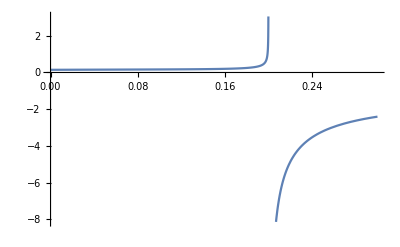

```mathematica
(* ============================================================================================ *)
GC2a[Gam_,  om0_,omc_,kap_,sig_ ]:=Evaluate[FullSimplify[G/.Solve[FullSimplify[eig/.Solve[FullSimplify[PowerExpand[FullSimplify[Det[OptMat2-Id2 eig]]]]==0,eig][[1]]]==0,G][[1]]]]
GC2b[lam_]:=Evaluate[ GC2a[GammaD+lam, omega0,omegac,kappaD,sigzf[lam]]];
(* ============================================================================================ *)
Plot[Re[GC2b[lam]],{lam,0,GammaD+0.1}]
(* ============================================================================================ *)
```

(-kap/2-ⅈ omc | 0 | -ⅈ G | -ⅈ G
0 | -kap/2+ⅈ omc | ⅈ G | ⅈ G
ⅈ G sig | ⅈ G sig | 1/2 (-Gam-lam)+ⅈ om0 | 0
-ⅈ G sig | -ⅈ G sig | 0 | 1/2 (-Gam-lam)-ⅈ om0)

Determinant: 1/16 ((Gam+lam)^2+4 om0^2) (kap^2+4 omc^2)-4 G^2 om0 omc sig

Det Zero 1: -(√((Gam+lam)^2+4 om0^2) √(kap^2+4 omc^2))/(8 √om0 √omc √sig)

Det Zero 2: (√((Gam+lam)^2+4 om0^2) √(kap^2+4 omc^2))/(8 √om0 √omc √sig)

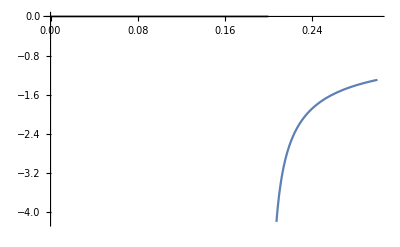

```mathematica
(* ============================================================================================ *)
OptMat3 ={{ -I omc -kap/2, 0, -I G, - I G  },{0, I omc -kap/2,  I G , I G },{I sig G,I sig G,I om0-(Gam + lam)/2 , 0 }, { -I sig G, -I sig G, 0, -I om0-(Gam + lam)/2}};
Id4 ={{ 1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
OptMat3//MatrixForm
Print["Determinant: ",FullSimplify[Det[OptMat3]]];
(*Print["Eig 1: ",FullSimplify[G/.Solve[FullSimplify[eig/.Solve[FullSimplify[PowerExpand[FullSimplify[Det[OptMat3-Id4 eig]]]]==0,eig][[1]]]==0,G][[1]]]];
Print["Eig 2: ",FullSimplify[G/.Solve[FullSimplify[eig/.Solve[FullSimplify[PowerExpand[FullSimplify[Det[OptMat3-Id4 eig]]]]==0,eig][[1]]]==0,G][[2]]]];*)
Print["Det Zero 1: ",FullSimplify[G/.Solve[FullSimplify[Det[OptMat3]]==0,G][[1]]]]
Print["Det Zero 2: ",FullSimplify[G/.Solve[FullSimplify[Det[OptMat3]]==0,G][[2]]]]
(* ============================================================================================ *)
GC3a[Gam_,  om0_,omc_,kap_,sig_ ]:=Evaluate[FullSimplify[G/.Solve[FullSimplify[Det[OptMat3]]==0,G][[1]]]]
GC3b[lam_]:=Evaluate[ GC3a[GammaD+lam, omega0,omegac,kappaD,sigzf[lam]]];
(* ============================================================================================ *)
Plot[Re[GC3b[lam]],{lam,0,GammaD+0.1}]
(* ============================================================================================ *)
```

(-kap/2-ⅈ omc | -ⅈ G | -ⅈ G
ⅈ G (-s12+sz1) | -GamT/2-ⅈ om0 | ⅈ EXP Om
ⅈ G (-s21+sz2) | (ⅈ Om)/EXP | -GamT/2-ⅈ om0)

Determinant: 1/8 (-(4 Om (EXP Om (kap+2 ⅈ omc)+2 ⅈ G^2 (s12-sz1)))/EXP-(GamT+2 ⅈ om0) ((GamT+2 ⅈ om0) (kap+2 ⅈ omc)+4 G^2 (s12-sz1))-4 G^2 (GamT+2 ⅈ (EXP Om+om0)) (s21-sz2))

Det Zero 1: -(2 ⅈ EXP GamT ((ⅈ G^2 (1+EXP^2-ⅈ EXP GamT+2 EXP om))/(2 EXP)+1/8 ⅈ (-ⅈ kap+2 om) (4+GamT^2+4 ⅈ GamT om-4 om^2)))/(3 G^2 (1+EXP^2-ⅈ EXP GamT+2 EXP om))

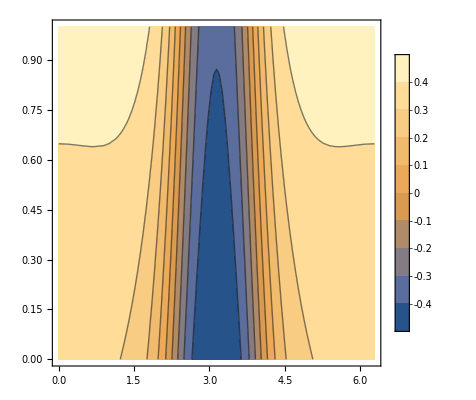

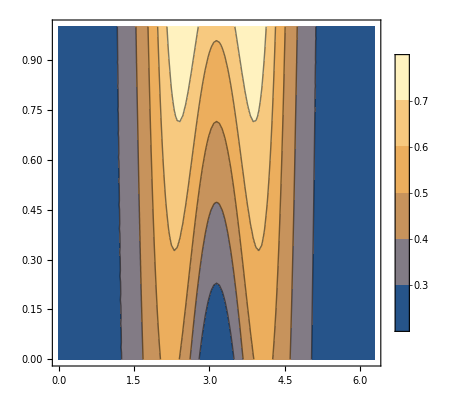

Det: 1/8 (-(4 Om (EXP Om (2 eig+kap+2 ⅈ omc)+2 ⅈ G^2 (s12-sz1)))/EXP-(2 eig+GamT+2 ⅈ om0) ((2 eig+GamT+2 ⅈ om0) (2 eig+kap+2 ⅈ omc)+4 G^2 (s12-sz1))-4 G^2 (2 eig+GamT+2 ⅈ (EXP Om+om0)) (s21-sz2))

Det w/ assumptions: -(8 eig^3 EXP GamT+EXP GamT (4+(GamT+2 ⅈ om)^2) (kap+2 ⅈ om)+4 eig^2 EXP GamT (2 GamT+kap+6 ⅈ om)+4 ⅈ G^2 (GamT-3 lam) (1+EXP (EXP-ⅈ GamT+2 om))+2 eig EXP (GamT^3-12 G^2 lam+2 GamT^2 (kap+4 ⅈ om)+4 GamT (1+G^2+ⅈ kap om-3 om^2)))/(8 EXP GamT)

```mathematica
(* ============================================================================================ *)

OptMat4 ={{ -I omc -kap/2, -I G,-I G },{I G(sz1-s12),-I om0-(GamT)/2 ,I Om EXP},{I G(sz2-s21),I Om (1/EXP),-I om0-(GamT)/2 }};
OptMat4//MatrixForm
OM4det = Evaluate[FullSimplify[Det[OptMat4]]];
OM4tr = Evaluate[FullSimplify[Tr[OptMat4]]];

Id3 ={{ 1,0,0},{0,1,0},{0,0,1 }};

OM4eig = Evaluate[FullSimplify[Det[OptMat4-Id3 eig]]];

Print["Determinant: ",OM4det];

(* ============================================================================================ *)
Sigma4=Evaluate[Solve[s12==(-I Om)/(lam + I  om21)(s11 - s22)&&s21==(I Om)/(lam - I  om21 )(s11 - s22)&&s11 ==Gam1/(GamT)+(I Om)/lam(s21 EXP - s12 (1/EXP))&&s22 ==Gam2/(GamT)-(I Om)/lam(s21 EXP - s12 (1/EXP)),{s11, s22, s12,s21 }]];
sigma00=lam/(GamT);
sigma11 =Evaluate[FullSimplify[PowerExpand[s11/.Sigma4[[1]][[1]]]]];
sigma22=Evaluate[FullSimplify[PowerExpand[s22/.Sigma4[[1]][[2]]]]];
sigma12=Evaluate[FullSimplify[PowerExpand[s12/.Sigma4[[1]][[3]]]]];
sigma21=Evaluate[FullSimplify[PowerExpand[s21/.Sigma4[[1]][[4]]]]];

(* ============================================================================================ *)
(* Determinant calculation *)

OM4DetFunc[Gam1_,Gam2_,omc_, om0_,kap_ ,s12_ ,s21_,sz1_,sz2_]:=Evaluate[Simplify[PowerExpand[FullSimplify[PowerExpand[FullSimplify[PowerExpand[OM4det]]]]]]];
OM4DetFunc2[lam_, GamT_, Gam1_,Gam2_,omc_, om0_,kap_,om21_,Om_]:=Evaluate[FullSimplify[Simplify[OM4DetFunc[Gam1, Gam2,omc, om0,kap ,sigma12 ,sigma21,sigma00 - sigma11,sigma00 - sigma22]]]];
OM4PureDet[lam_,kap_,GamT_,om_,EXP_,G_]:=Evaluate[FullSimplify[OM4DetFunc2[lam,GamT,(GamT-lam)/2,(GamT-lam)/2,om,om,kap,0,1]]];

OM4TrFunc[lam_, GamT_, Gam1_,Gam2_,omc_, om0_,kap_,om21_,Om_]:=Evaluate[Simplify[PowerExpand[FullSimplify[PowerExpand[FullSimplify[PowerExpand[OM4tr]]]]]]];
OM4PureTr[lam_,kap_,GamT_,om_,EXP_,G_]:=Evaluate[FullSimplify[OM4TrFunc[lam,GamT,(GamT-lam)/2,(GamT-lam)/2,om,om,kap,0,1]]];
(* ============================================================================================ *)

lam4a=Evaluate[Solve[Evaluate[Simplify[OM4DetFunc2[lam,GamT,(GamT-lam)/2,(GamT-lam)/2,om,om,kap,0,1]]]==0, lam]];
lam4b[ GamT_,kap_,om_,G_,EXP_]:=Evaluate[lam/.lam4a[[1]]]
Print["Det Zero 1: ",Evaluate[lam/.lam4a[[1]]]]
plotfunc[phi_,kap_]:=Evaluate[FullSimplify[PowerExpand[lam4b[1.0,kap,1.0,0.9,Exp[I*phi]]]]]
ContourPlot[Re[plotfunc[phi,kap]],{phi,0,2*Pi},{kap,0,1},PlotLegends->Automatic]
ContourPlot[Im[plotfunc[phi,kap]],{phi,0,2*Pi},{kap,0,1},PlotLegends->Automatic]

(* ============================================================================================ *)
(* Eigenvalue calculation *)

OM4EigFunc2a[s12_ ,s21_,sz1_,sz2_]:=Evaluate[FullSimplify[PowerExpand[Simplify[OM4eig]]]];
OM4EigFunc2b[lam_, GamT_, Gam1_,Gam2_,omc_, om0_,kap_,om21_,Om_,G_]:=Evaluate[FullSimplify[PowerExpand[Simplify[OM4EigFunc2a[sigma12 ,sigma21,sigma00 - sigma11,sigma00 - sigma22]]]]];

OM4EigFunc2c[lam_,GamT_,om_,kap_,EXP_,G_]:=Evaluate[FullSimplify[PowerExpand[OM4EigFunc2b[lam, GamT, (GamT-lam)/2,(GamT-lam)/2, om, om,kap,0,1,G]]]];
Print["Det: ", OM4eig]
Print["Det w/ assumptions: ",OM4EigFunc2c[lam,GamT,om,kap, EXP,G]];
```

```mathematica
SimpEigFunc[eig_,lam_,EXP_]:=Evaluate[FullSimplify[OM4EigFunc2c[lam,1,1,1, EXP,1]]]
OptMatDem[eig_,lam_,phi_]:=Evaluate[Collect[FullSimplify[Collect[SimpEigFunc[eig,lam,Exp[I phi]],eig]],eig]]
PhasePoint[lam_,phi_]:=FullSimplify[Discriminant[FullSimplify[OptMatDem[eig,lam,phi]],eig]]
Plot3D[PhasePoint[lam,phi],{phi,0,2*Pi},{lam,0,1},PlotRange->{{0,2*Pi},{0,1},{-2,2}}]
PhasePoint[lam,phi]
```

-Graphics3D-

```mathematica
(* ==================================================================================== *)
```

4 (-2+3 lam)^3+27 (1-3 lam)^2 Cos[phi]^2

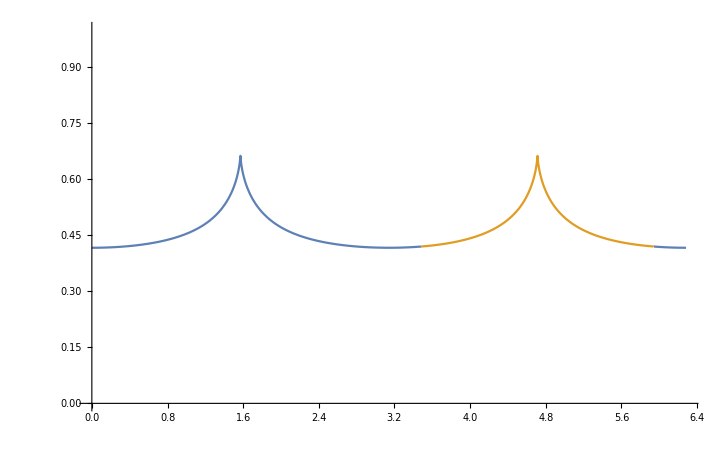

```mathematica
f1[phi_]:=1/12 (8-9 Cos[phi]^2-(24 Cos[phi]^2)/((Cos[phi]^2 (-8+36 Cos[phi]^2-27 Cos[phi]^4+8 Sin[phi]))^(1/3))+(27 Cos[phi]^4)/((Cos[phi]^2 (-8+36 Cos[phi]^2-27 Cos[phi]^4+8 Sin[phi]))^(1/3))+3 (Cos[phi]^2 (-8+36 Cos[phi]^2-27 Cos[phi]^4+8 Sin[phi]))^(1/3));
f2[phi_]:=1/24 (16-18 Cos[phi]^2+((-3-3 ⅈ √3) Cos[phi]^2 (-8+9 Cos[phi]^2))/((Cos[phi]^2 (-8+36 Cos[phi]^2-27 Cos[phi]^4+8 Sin[phi]))^(1/3))+3 ⅈ (ⅈ+√3) (Cos[phi]^2 (-8+36 Cos[phi]^2-27 Cos[phi]^4+8 Sin[phi]))^(1/3));
f3[phi_]:=1/24 (16-18 Cos[phi]^2+(3 ⅈ (ⅈ+√3) Cos[phi]^2 (-8+9 Cos[phi]^2))/((Cos[phi]^2 (-8+36 Cos[phi]^2-27 Cos[phi]^4+8 Sin[phi]))^(1/3))-3 (1+ⅈ √3) (Cos[phi]^2 (-8+36 Cos[phi]^2-27 Cos[phi]^4+8 Sin[phi]))^(1/3));

Plot[{f1[phi],f2[phi],f3[phi]},{phi,0,2*Pi},PlotRange->{{0,2*Pi},{0,1}}]
```

```mathematica
kapval2=1;
Eig3Plot[EXP_,lam_]:=Evaluate[OM4EigFunc2c[lam,1,1,1,EXP,1]];
Eig1PlotSolve[phi2_,lam_]:=Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I phi2], lam]]==0,eig][[1]]]
Eig2PlotSolve[phi2_,lam_]:=Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I phi2], lam]]==0,eig][[2]]]
Eig3PlotSolve[phi2_,lam_]:=Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I phi2], lam]]==0,eig][[3]]]
Plot3D[Eig3PlotSolve[phi2,lam],{phi2,0,2*Pi},{lam,0,1},PlotRange->{{0,2*Pi},{0,1},{0,1}}]
```

-Graphics3D-

```mathematica
(* ==================================================================================== *)
```

{{lam→2/3},{lam→2/3},{lam→2/3}}

{{lam→-1/3},{lam→-1/3},{lam→5/12}}

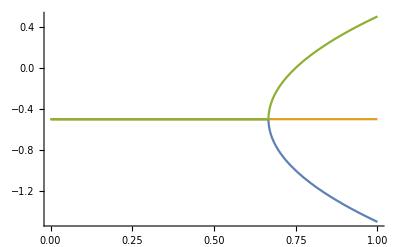

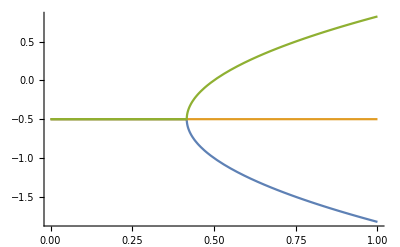

```mathematica
FullSimplify[Solve[PhasePoint[lam,Pi/2]==0,lam]]
FullSimplify[Solve[PhasePoint[lam,0]==0,lam]]

Eig3Plot[EXP_,lam_]:=Evaluate[OM4EigFunc2c[lam,1,1,1,EXP,1]];

Plot[{Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I Pi/2], lam]]==0,eig][[1]]],Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I Pi/2], lam]]==0,eig][[2]]],Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I Pi/2], lam]]==0,eig][[3]]]},{lam,0,1},PlotRange->All]

Plot[{Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I 0], lam]]==0,eig][[1]]],Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I Pi/2], lam]]==0,eig][[2]]],Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I 0], lam]]==0,eig][[3]]]},{lam,0,1},PlotRange->All]
```

```mathematica
(* ==================================================================================== *)
Print["***************** phi = Pi/2 *****************"]

X1=C0;
X2=C0 + X ;
X3=C0 - X;
FullSimplify[((X1 - X2)(X1-X3)(X2-X3))^2]

FullSimplify[OM4EigFunc2c[lam,1,1,1,Exp[I Pi/2],g]]
FullSimplify[Discriminant[OM4EigFunc2c[lam ,1,1,1,Exp[I Pi/2],g],eig]]
FullSimplify[Solve[Discriminant[OM4EigFunc2c[lam ,1,1,1,Exp[I Pi/2],g],eig]==0,lam]]
FullSimplify[Solve[((1/4)Discriminant[OM4EigFunc2c[lam ,1,1,1,Exp[I Pi/2],g],eig])^(1/6)==1/2,lam]]
(* ==================================================================================== *)
Print["***************** phi = 0 *****************"]

X1=C0;
X2=C0 + (X + I Y );
X3=C0 - (X  - I Y);
FullSimplify[((X1 - X2)(X1-X3)(X2-X3))^2]

FullSimplify[OM4EigFunc2c[lam,1,1,1,Exp[I 0],g]]
FullSimplify[Discriminant[OM4EigFunc2c[lam ,1,1,1,Exp[I 0],g],eig]]

Solve[(4(3*u-1)+-1)^(2/4)==0,u]
Solve[Simplify[Re[ComplexExpand[(-1+4(-1+3 u))^(2/4)]]-(1/2),u≥0]==0,u]
Solve[Simplify[Re[ComplexExpand[(1/2)(4(3*u-1)+-1)^(2/4)]],u≥0]==1/2,u]
(* ==================================================================================== *)
```

***************** phi = Pi/2 *****************

4 X^6

-1/8 ((1+2 ⅈ)+2 eig) ((1+4 ⅈ)+4 eig ((1+2 ⅈ)+eig)+g^2 (4-12 lam))

4 (-1+g^2 (-1+3 lam))^3

{{lam→1/3 (1+1/g^2)},{lam→1/3 (1+1/g^2)},{lam→1/3 (1+1/g^2)}}

{{lam→1/3+5/(12 g^2)},{lam→1/24 (8+(7-ⅈ √3)/g^2)},{lam→1/24 (8+(7+ⅈ √3)/g^2)}}

***************** phi = 0 *****************

4 X^2 (X^2+Y^2)^2

-1/8 ((1+4 ⅈ)+2 eig) ((1+2 ⅈ)+4 eig ((1+ⅈ)+eig)+g^2 (4-12 lam))

(2+g^2 (-1+3 lam))^2 (-1+4 g^2 (-1+3 lam))

{{u→5/12}}

{{u→7/16}}

{{u→1/2}}

```mathematica
(* ==================================================================================== *)
```

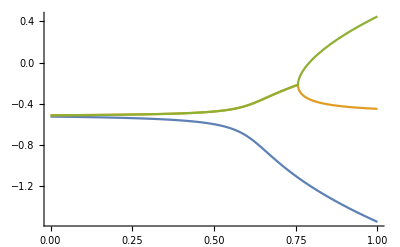

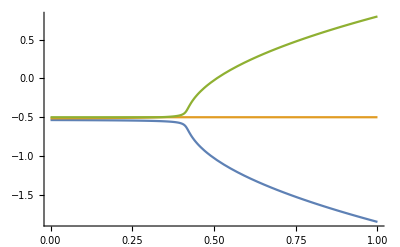

```mathematica
Eig3Plot[EXP_,lam_]:=Evaluate[OM4EigFunc2c[lam,1,1,1.1,EXP,1]];

Plot[{Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I Pi/2], lam]]==0,eig][[1]]],Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I Pi/2], lam]]==0,eig][[2]]],Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I Pi/2], lam]]==0,eig][[3]]]},{lam,0,1},PlotRange->All]

Plot[{Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I 0], lam]]==0,eig][[1]]],Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I 0], lam]]==0,eig][[2]]],Re[eig/.Solve[Evaluate[Eig3Plot[Exp[I 0], lam]]==0,eig][[3]]]},{lam,0,1},PlotRange->All]
```

```mathematica
(* ======================================================================================== *)
X1=C0- X;
X2=C0+X+Y1;
X3=C0+X+ Y2;
FullSimplify[PowerExpand[FullSimplify[((X1 - X2)(X1-X3)(X2-X3))^2]]]
```

(2 X+Y1)^2 (Y1-Y2)^2 (2 X+Y2)^2

```mathematica
OM4EigFunc2c[lam,GamT,om,kap, EXP,G]
```

```mathematica
KapVar1[EXP_,GamT_,kappa_]:=Evaluate[OM4EigFunc2c[GamT,GamT,GamT,kappa,EXP,1]];
KapVar2[EXP_,GamT_,kappa_]:=Evaluate[OM4EigFunc2c[kappa,GamT,GamT,kappa,EXP,1]];
FullSimplify[Discriminant[FullSimplify[KapVar1[Exp[I Pi/2],GamT,kappa]],eig]]
FullSimplify[Discriminant[FullSimplify[KapVar1[Exp[I 0],GamT,kappa]],eig]]
FullSimplify[Discriminant[FullSimplify[KapVar2[Exp[I Pi/2],GamT,kappa]],eig]]
FullSimplify[Discriminant[FullSimplify[KapVar2[Exp[I 0],GamT,kappa]],eig]]
```

4-1/4 (44+(GamT-kappa)^2) (GamT-kappa)^2

-1/4 (4 ⅈ+GamT-kappa)^2 (28+GamT^2-2 GamT (2 ⅈ+kappa)+kappa (4 ⅈ+kappa))

1/(4 GamT^3)(-GamT^7+4 GamT^6 kappa+432 kappa^3+12 GamT^2 kappa (48-7 kappa^2)+GamT^5 (13-6 kappa^2)+9 GamT kappa^2 (-96+kappa^2)+4 GamT^4 kappa (-23+kappa^2)-GamT^3 (128-154 kappa^2+kappa^4))

-((GamT (ⅈ+GamT-kappa)+3 ⅈ kappa)^2 (GamT ((-4-2 ⅈ)+GamT-kappa) ((4-2 ⅈ)+GamT-kappa)+48 kappa))/(4 GamT^3)

```mathematica
Test1
```

Test1

1/4 ((-1-2 ⅈ)-kappa+√((29-4 ⅈ)+((-2+4 ⅈ)+kappa) kappa))

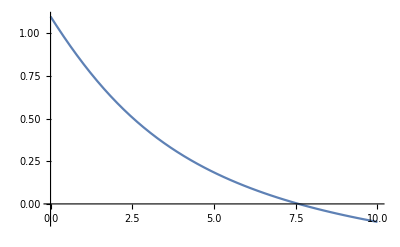

0.-0.116435 ⅈ

-2-√(-((GamT+kappa)^2 (-8+GamT kappa))/(GamT kappa))

7.58826

```mathematica
(* ======================================================================================== *)

$Assumptions=Element[kappa,Reals];
Rad1[GamT_,kappa_]:=eig/.FullSimplify[Solve[FullSimplify[KapVar1[Exp[I 0],GamT,kappa]]==0,eig]][[3]]
Kap1Root1[GamT_,kappa_]:=FullSimplify[Rad1[GamT,kappa],Assumptions->{GamT≥0,kappa≥0}]
Kap1Root1[1,kappa]
Plot[Re[Test1[1,kappa]],{kappa,0,10}]
Test1[1,7.588488679643104]
Simplify[Reduce[Re[Kap1Root1[GamT,kappa]]==0&&GamT≥0,kappa][[2]][[2]][[1]][[2]][[1]][[2]],kappa≥0]
Kap1Root1Reduction1[GamT_,kappa_]:=Evaluate[Simplify[Reduce[Re[Kap1Root1[GamT,kappa]]==0&&GamT≥0,kappa][[2]][[2]][[1]][[2]][[1]][[2]],kappa≥0]]
Kap1Root1Reduction2[GamT_]:=Evaluate[Normal[FullSimplify[PowerExpand[Series[kappa/.FullSimplify[PowerExpand[Solve[Kap1Root1Reduction1[GamT,kappa]==0,kappa][[1]]]],{GamT,0,8}]]]]]
N[Kap1Root1Reduction2[1]]
```

```mathematica
(* ======================================================================================== *)
X1=C0- X;
X2=C0+X+Y1;
X3=C0+X+ Y2;
FullSimplify[X1 + X2 + X 2]
FullSimplify[PowerExpand[FullSimplify[((X1 - X2)(X1-X3)(X2-X3))^2]]]
```

0.-0.116435 ⅈ

-2-√(-((GamT+kappa)^2 (-8+GamT kappa))/(GamT kappa))

7.58826

```mathematica
Solve[8/GamT-GamT/2==kap,GamT]
```

{{GamT→-kap-√(16+kap^2)},{GamT→-kap+√(16+kap^2)}}

```mathematica
Rad2[GamT_,kappa_]:=eig/.FullSimplify[Solve[FullSimplify[KapVar1[Exp[I Pi/2],GamT,kappa]]==0,eig]][[1]]
Kap2Root1[GamT_,kappa_]:=FullSimplify[Rad2[GamT,kappa],Assumptions->{GamT≥0,kappa≥0}]
Kap2Root1[GamT,kappa]
```

1/96 (-16 ((2+6 ⅈ) GamT+kappa)-(16 (12+(GamT-kappa)^2))/((-GamT^3+6 √3 √(-16+44 (GamT-kappa)^2+(GamT-kappa)^4)+72 kappa+3 GamT^2 kappa+kappa^3-3 GamT (24+kappa^2))^(1/3))-16 (-GamT^3+6 √3 √(-16+44 (GamT-kappa)^2+(GamT-kappa)^4)+72 kappa+3 GamT^2 kappa+kappa^3-3 GamT (24+kappa^2))^(1/3))

```mathematica
Simplify[Reduce[Kap2Root1[GamT,kappa]==0&&GamT≥0,kappa],kappa≥0]
```

$Aborted

```mathematica
Kap1Sol[GamT_,kappa_]:=Evaluate[eig/.FullSimplify[Solve[FullSimplify[KapVar1[Exp[I Pi/2],GamT,kappa]]==0,eig]]]
```

(-1-3 ⅈ) GamT-kappa/2

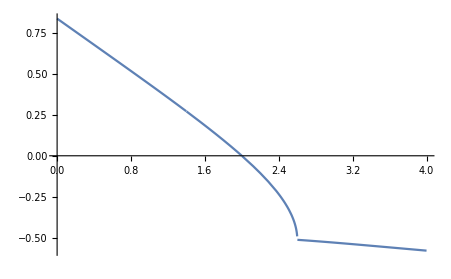

$Aborted

```mathematica
Plot[Re[Kap1Sol[2,kappa][[2]]],{kappa,0,4}]
```

```mathematica
Rad2[GamT_,kappa_]:=Evaluate[eig/.FullSimplify[Solve[FullSimplify[KapVar1[Exp[I Pi/2],GamT,kappa]]==0,eig]][[2]]]
Rad2[1,kappa]
```

$Aborted

1/96 (-16 ((2+6 ⅈ)+kappa)-(16 (12+(1-kappa)^2))/((-1+6 √3 √(-16+44 (1-kappa)^2+(1-kappa)^4)+75 kappa+kappa^3-3 (24+kappa^2))^(1/3))-16 (-1+6 √3 √(-16+44 (1-kappa)^2+(1-kappa)^4)+75 kappa+kappa^3-3 (24+kappa^2))^(1/3))

```mathematica
FullSimplify[ComplexExpand[Re[Evaluate[Kap1Sol[GamT,kappa][[2]]]]],{GamT≥0,kappa≥0}]
```

1/12 Re[-2 ((2+6 ⅈ) GamT+kappa)+((1+ⅈ √3) (12+(GamT-kappa)^2))/((-GamT^3+6 √3 √(-16+44 (GamT-kappa)^2+(GamT-kappa)^4)+72 kappa+3 GamT^2 kappa+kappa^3-3 GamT (24+kappa^2))^(1/3))+(1-ⅈ √3) (-GamT^3+6 √3 √(-16+44 (GamT-kappa)^2+(GamT-kappa)^4)+72 kappa+3 GamT^2 kappa+kappa^3-3 GamT (24+kappa^2))^(1/3)]

```mathematica
Re[Kap1Sol[2,kappa][[2]]]
```

```mathematica
N[Kap1Root1Reduction2[2]]
```

3.42188

```mathematica
Solve[FullSimplify[Discriminant[FullSimplify[KapVar1[Exp[I Pi/2],GamT,kappa]],eig]]==3/4,kappa]
```

{{kappa→-√(-22+√497)+GamT},{kappa→√(-22+√497)+GamT},{kappa→-ⅈ √(22+√497)+GamT},{kappa→ⅈ √(22+√497)+GamT}}

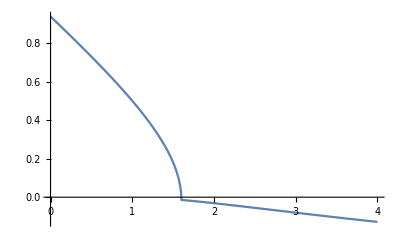

```mathematica
Plot[Re[Kap2Root1[1,kappa]],{kappa,0,4}]
```

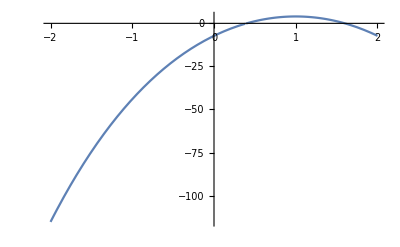

```mathematica
Plot[FullSimplify[Discriminant[FullSimplify[KapVar1[Exp[I Pi/2],1,kappa]],eig]],{kappa,-2,2}]
```

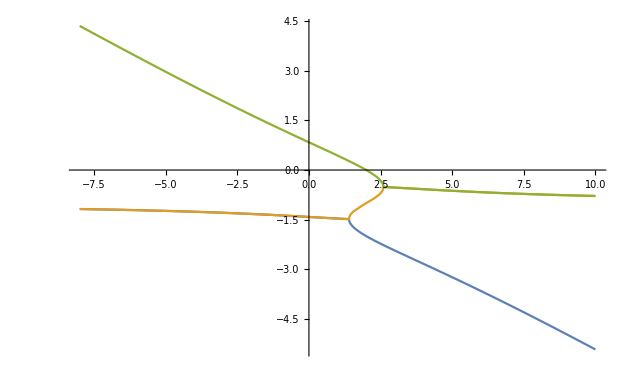

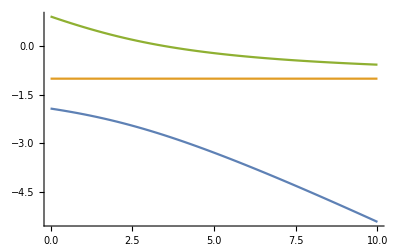

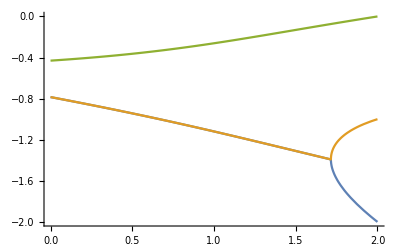

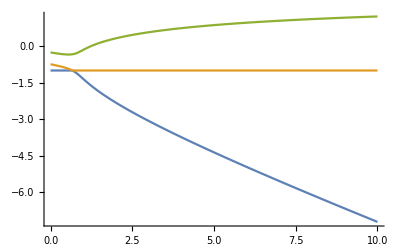

```mathematica
(* ======================================================================================== *)
(* Plots of the above *)
GamTvar = 2.0;
Plot[{Re[eig/.Solve[Evaluate[KapVar1[Exp[I Pi/2], GamTvar, kappa]]==0,eig][[1]]],Re[eig/.Solve[Evaluate[KapVar1[Exp[I Pi/2],GamTvar,kappa]]==0,eig][[2]]],Re[eig/.Solve[Evaluate[KapVar1[Exp[I Pi/2],GamTvar, kappa]]==0,eig][[3]]]},{kappa,-8,10},PlotRange->All]

Plot[{Re[eig/.Solve[Evaluate[KapVar1[Exp[I 0],GamTvar, kappa]]==0,eig][[1]]],Re[eig/.Solve[Evaluate[KapVar1[Exp[I 0],GamTvar,kappa]]==0,eig][[2]]],Re[eig/.Solve[Evaluate[KapVar1[Exp[I 0],GamTvar, kappa]]==0,eig][[3]]]},{kappa,0,10},PlotRange->All]

Plot[{Re[eig/.Solve[Evaluate[KapVar2[Exp[I Pi/2], GamTvar, kappa]]==0,eig][[1]]],Re[eig/.Solve[Evaluate[KapVar2[Exp[I Pi/2],GamTvar,kappa]]==0,eig][[2]]],Re[eig/.Solve[Evaluate[KapVar2[Exp[I Pi/2],GamTvar, kappa]]==0,eig][[3]]]},{kappa,0,2},PlotRange->All]

Plot[{Re[eig/.Solve[Evaluate[KapVar2[Exp[I 0],GamTvar, kappa]]==0,eig][[1]]],Re[eig/.Solve[Evaluate[KapVar2[Exp[I 0],GamTvar,kappa]]==0,eig][[2]]],Re[eig/.Solve[Evaluate[KapVar2[Exp[I 0],GamTvar, kappa]]==0,eig][[3]]]},{kappa,0,10},PlotRange->All]
```

```mathematica
(* ======================================================================================== *)

FuncDlam[r_,x_]:=r(x+(1/2))-(x+(1/2))^3
FuncDlamDx[r_,x_]:=D[FuncDlam[r,x],x]
LamFunc[r_,x_]:=Evaluate[FullSimplify[Integrate[1/FuncDlam[r,x],x]]]
LamFuncX[r_,lam_]:=x/.Normal[Solve[LamFunc[r,x]==lam,x]][[1]]

Print["x value for zero lam gradient (gradient asymptote): ", FullSimplify[Solve[FuncDlamDx[r,x]==0,x]]]
Print["lam gradient at gradient asymptote (linear pumping): ",FullSimplify[FuncDlam[r,-1/2-(√r)/(√3)]]]
Print["lam gradient at x-intercept: ",FullSimplify[FuncDlam[r,0]]]

(* ======================================================================================== *)
```

x value for zero lam gradient (gradient asymptote): {{x→-1/2-(√r)/(√3)},{x→-1/2+(√r)/(√3)}}

lam gradient at gradient asymptote (linear pumping): -(2 r^(3/2))/(3 √3)

lam gradient at x-intercept: 1/8 (-1+4 r)

```mathematica
PDFunc[r_,x_,dx_]:=FuncDlam[r,x+dx]
Normal[Series[PDFunc[r,-1/2,dx],{dx,0,3}]]
dxsol[lam_,r_]:=Evaluate[dx/.Normal[Solve[Integrate[1/Normal[Series[PDFunc[r,-1/2,dx],{dx,0,1}]],dx]==lam-(1/2)]][[1]]]
dxsol[lam,r]
```

-dx^3+dx r

ⅇ^(1/2 (-1+2 lam) r)

```mathematica
dxsol[lam_,r_]:=Evaluate[dx/.Normal[Solve[Integrate[1/Normal[Series[PDFunc[r,-1/2,dx],{dx,0,1}]],dx]==lam-(1/2)]][[1]]]
rval1=Evaluate[r/.Normal[Solve[dxsol[5/12,r]==1/2,r]][[1]]];
dxsol[lam_,r_]:=Evaluate[dx/.Normal[Solve[Integrate[1/Normal[Series[PDFunc[r,-1/2,dx],{dx,0,1}]],dx]==lam-(3/4)]][[1]]]
rval2=Evaluate[r/.Normal[Solve[dxsol[2/3,r]==1/2,r]][[1]]];
rval1
rval2
```

12 (2 ⅈ π C[1]+Log[2])

12 (2 ⅈ π C[1]+Log[2])